## Modelo contínuo do sistema

```mathematica
A = {{-0.2,0},{1,0}};
```

```mathematica
B={{10},{0}};
```

```mathematica
Cs={{0,1}};
```

```mathematica
Ds={{0}};
```

```mathematica
SS=StateSpaceModel[{A,B,Cs,Ds}]
```

(-0.2 | 0 | 10
1 | 0 | 0
0 | 1 | 0)_^𝒮

## Modelo discreto do sistema

```mathematica
SSd = ToDiscreteTimeModel[SS,Ts,Method->"ForwardRectangularRule"]
```

(1-0.2 Ts | 0 | 10 Ts
Ts | 1 | 0
0 | 1 | 0)_Ts^𝒮

## Ganhos do observador

```mathematica
FullSimplify[EstimatorGains[SSd,{0.5,0.6}]]
```

{{-0.18+0.2/Ts+0.04 Ts},{0.9-0.2 Ts}}

## Análise de estabilidade

```mathematica
roots = Solve[TransferFunctionModel[SSd][[1]][[2]]==0,z]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{z→1.},{z→0.2 (5.-1. Ts)}}

### Primeiro pólo

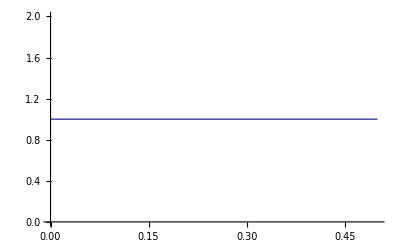

```mathematica
Plot[z/.roots[[1]],{Ts,0,0.5}]
```

### Segundo pólo

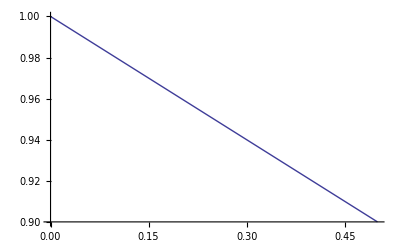

```mathematica
Plot[z/.roots[[2]],{Ts,0,0.5}]
```